```mathematica
mF[f_] := {{1, 0}, {-1/f, 1}}(* dünne Linse *)
```

```mathematica
m0[L_] := {{1, L}, {0, 1}} (* Driftmatrix *)
```

```mathematica
mM:= {{Cos[ϕ]+α*Sin[ϕ],β*Sin[ϕ]},{-(1+α^2)/β*Sin[ϕ],Cos[ϕ]-α*Sin[ϕ]}} (* Twiss-Matrix *)
```

```mathematica
mM//MatrixForm
```

(Cos[ϕ]+α Sin[ϕ] | β Sin[ϕ]
-((1+α^2) Sin[ϕ])/β | Cos[ϕ]-α Sin[ϕ])

Die gesamte FODO-Struktur in 2 Teile “splitten”. Zuerst hat man den FOD Teil und dann den DOF Teil. Diese dann miteinander multiplizieren.

```mathematica
fod=mF[-f].m0[L]. (mF[f])
```

{{1-L/f,L},{1/f-(1+L/f)/f,1+L/f}}

```mathematica
dof=mF[f].m0[L].mF[-f]
```

{{1+L/f,L},{-1/f+(1-L/f)/f,1-L/f}}

```mathematica
fodo=dof.fod//FullSimplify
```

{{1-(2 L^2)/f^2,(2 L (f+L))/f},{(2 L (-f+L))/f^3,1-(2 L^2)/f^2}}

```mathematica
muh=Tr[mM]==Tr[fodo]
```

2 Cos[ϕ]==2-(4 L^2)/f^2

```mathematica
Solve[muh,ϕ]//Simplify//.L^2/f^2-> 1/κ^2
```

{{ϕ→ConditionalExpression[-ArcCos[1-(2 L^2)/f^2]+2 π C[1],C[1]∈ℤ]},{ϕ→ConditionalExpression[ArcCos[1-(2 L^2)/f^2]+2 π C[1],C[1]∈ℤ]}}

```mathematica
phi=ϕ-> ArcCos[1-2/κ^2]
```

ϕ→ArcCos[1-2/κ^2]

Für β gilt die Betatronfunktion: β = C^2*β0-2*S*C*α0+S^2*γ0. Mit γ0=1/β0, β0=β und α0=0. α0=0 kommt daher wenn man die Diagonaleinträge der Twissmatrix mit denen der FODO-Matrix vergleicht. Beide Werte in der Fodo-Matrix sind gleich, somit muss α0=0 sein damit das erfüllt ist.

Für das maximale β gilt:

```mathematica
betamax=Solve[β== (fodo[[1,1]])^2*β+(fodo[[1,2]])^2*1/β,β][[2]]
```

{β→(2 f (f+L))/(√(4 f^2-4 L^2))}

```mathematica
betamaxk = β-> L*(κ*(κ+1))/(√(κ^2-1))
```

β→(L κ (1+κ))/(√(-1+κ^2))

Für das minimale β gilt:

```mathematica
dofo=fod.dof//FullSimplify
```

{{1-(2 L^2)/f^2,2 L (1-L/f)},{-(2 L (f+L))/f^3,1-(2 L^2)/f^2}}

```mathematica
betamin=Solve[β== (dofo[[1,1]])^2*β+(dofo[[1,2]])^2*1/β,β][[2]]//FullSimplify
```

{β→(√(f^2 (f-L)^2))/(√(f^2-L^2))}

```mathematica
betamink=β-> L*(κ*(κ-1))/(√(κ^2-1))
```

β→(L (-1+κ) κ)/(√(-1+κ^2))

β→(L (-1+κ) κ)/(√(-1+κ^2))

Nun bestimmen wir unser κ damit β minimal wird.

Zunächst für die maximale β-Funktion.

```mathematica
kappamax=Solve[0== D[β//.betamaxk,κ]][[3]]
```

{κ→1/2 (1+√5)}

```mathematica
testmax=D[β//.betamaxk,{κ,2}]//FullSimplify
```

(L (2+κ) √(-1+κ^2))/((-1+κ)^3 (1+κ)^2)

```mathematica
testmax//.kappamax//FullSimplify
```

√(5/2 (1+√5)) L

Bestimme nun die Phase:

```mathematica
phimax=ϕ//.phi//.kappamax//N
```

1.33248

Die dritte Lösung für κ ist >0 und liefert somit das minimalste beta.

Nun bestimmen wir das κ für den Mittelwert.

```mathematica
betamittel=1/2*((β//.betamaxk)+(β//.betamink))//FullSimplify
```

(L κ^2)/(√(-1+κ^2))

```mathematica
betamit= β-> betamittel
```

β→(L κ^2)/(√(-1+κ^2))

```mathematica
kappamittel=Solve[0== D[β//.betamit,κ]][[4]]
```

{κ→√2}

```mathematica
testmit=D[β//.betamit,{κ,2}]//FullSimplify
```

(L (2+κ^2))/((-1+κ^2)^(5/2))

```mathematica
testmit//.kappamittel//FullSimplify
```

4 L

Bestimme nun die Phase:

```mathematica
phimit=ϕ//.phi//.kappamittel
```

π/2

Auch hier soll κ positiv sein, somit ist die 4. Lösung die richtige.

β oszilliert zwischen:

```mathematica
βmax = β//.betamaxk//.kappamittel//FullSimplify
```

(2+√2) L

```mathematica
βmin = β//.betamink//.kappamittel//FullSimplify
```

-(-2+√2) L

Der Mittelwert ist also

```mathematica
1/2(βmax+ βmin) //FullSimplify
```

2 L

Der Verlauf der β-Funktion innerhalb einer FODO-Zelle ist also

```mathematica
β[s_] = (2-√2)*L + 2 √2 Abs[L -s]
```

(2-√2) L+2 √2 Abs[L-s]

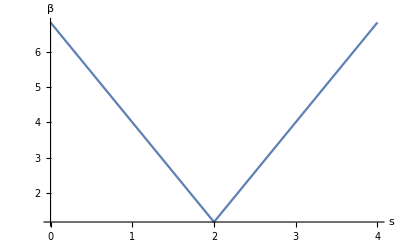

```mathematica
Plot[β[s] //.L->2, {s, 0, 4},  AxesLabel->{"s", "β"}]
```